(ẋ)_1=1/(m1+m2+mb)(2 g (2 m1+m2-mb) t μ+A0 ω (2 m2 Cos[γ]+(m1+m2+mb) Cos[t ω]-(m1-m2+mb) Cos[γ+t ω]))
x_1=(g (2 m1+m2-mb) t^2 μ+2 A0 m2 (t ω Cos[γ]-Sin[γ]+Sin[γ+t ω]))/(m1+m2+mb)
The distance mass b moves in one nudge is x_1 at the first time that(ẋ)_1=0.

```mathematica
Clear[A0,ω,m,m1,m2,g,μ,γ,mr,mb,i]
A0=.05;
ω=2 π 3;
m=.034;
γ=.25π;
m1=(3m)/34;
m2=(28m)/34;
g=9.81;
μ=.37;
T=120;
f=3.5;
λ1=.76;
λ2=1-λ1;
ϕ=π/5;
its=2;
```

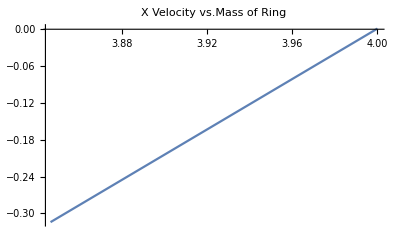

```mathematica
Ai=Range[its];
For[i=0,i<its,i++,
mr=.25m+i.01 m;
mb=mr;
s1=FindRoot[2 (g (2 m1+m2-mb) t μ+A0 m2 ω Cos[γ+t ω]),{t,.0006}];
τ=t/.s1;
If[τ>1/ω(π/2-γ),
τ=1/ω(π/2-γ);
];
Ai⟦i⟧=(g (2 m1+m2-mb) t^2 μ+2 A0 m2 Sin[γ+t ω])/(m1+m2+mb)-(2 A0 m2 Sin[γ])/(m1+m2+mb)/.t->τ;
];
Bi=Range[its];
For[i=0,i<its,i++,
mr=.25m+i.01 m;
mb=mr+m;
s1=FindRoot[2 (g (2 m1+m2-mb) t μ+A0 m2 ω Cos[γ+t ω]),{t,.0006}];
τ=t/.s1;
If[τ>1/ω(π/2-γ),
τ=1/ω(π/2-γ);
];
Bi⟦i⟧=(g (2 m1+m2-mb) t^2 μ+2 A0 m2 Sin[γ+t ω])/(m1+m2+mb)-(2 A0 m2 Sin[γ])/(m1+m2+mb)/.t->τ];


xx={};
xx2={};
xx3={};
xx4={};
xx5={};
For[i=0,i<its,i++,
A=Ai⟦i+1⟧;
B=Bi⟦i+1⟧;

AppendTo[xx,{.25m+.01*i m,-f((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/π}];
AppendTo[xx2,{1/(.25+i*.01),-f((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/π}];
AppendTo[xx3,{1/(.25+i*.01),-f/(4 π^3 T)(-4 A B λ1 (1+2 λ1) (π+ϕ-λ1 ϕ)-B^2 λ1 (π^3-6 π λ1+2 π^2 ϕ+6 (-1+λ1) λ1 ϕ)+A^2 (π^3 (-2+λ1)+π (2+4 λ1^2)+2 π^2 ϕ-2 (-1+λ1) (1+2 λ1^2) ϕ)-2 (A-B λ1) (π+ϕ-λ1 ϕ) ((A-B λ1) Cos[2 ϕ]+4 (A-B) λ1 Sin[ϕ])+π^2 (A^2-B^2 λ1) Sin[2 ϕ])}];
AppendTo[xx4,{1/(.25+i*.01),f(B^2 λ1 (π+2 ϕ)-A^2 (π (-2+λ1)+2 ϕ)+(A^2-B^2 λ1) Sin[2 ϕ])/(4 π T)}];
AppendTo[xx5,{1/(.25+i*.01),(f(B^2 λ1 (π+2 ϕ)-A^2 (π (-2+λ1)+2 ϕ)+(A^2-B^2 λ1) Sin[2 ϕ])/(4 π T))/(-f/(4 π^3 T)(-4 A B λ1 (1+2 λ1) (π+ϕ-λ1 ϕ)-B^2 λ1 (π^3-6 π λ1+2 π^2 ϕ+6 (-1+λ1) λ1 ϕ)+A^2 (π^3 (-2+λ1)+π (2+4 λ1^2)+2 π^2 ϕ-2 (-1+λ1) (1+2 λ1^2) ϕ)-2 (A-B λ1) (π+ϕ-λ1 ϕ) ((A-B λ1) Cos[2 ϕ]+4 (A-B) λ1 Sin[ϕ])+π^2 (A^2-B^2 λ1) Sin[2 ϕ]))}];
];

ListLinePlot[xx2,PlotRange->All,PlotLabel->"X Velocity vs.Mass of Ring"]
```

```mathematica
xx2
```

{{4.,0.00108391},{3.84615,-0.314324}}